```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Manual constructing a ruleset to create a specified n-dimensional network

#### Constructing a constant-width band (1-d case): one rule that creates a diagonal path across a SSS, creating and destroying a series of cells, and would die out without another rule to start over. Here the number of As defines the width of the band, but the band remains one-dimensional.



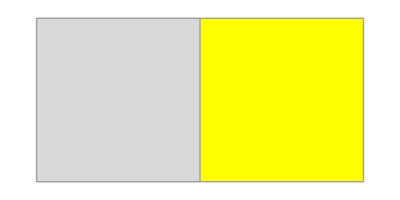
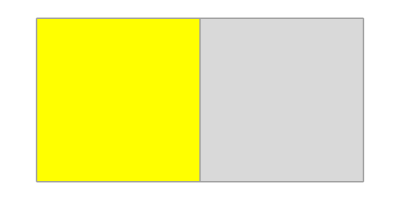
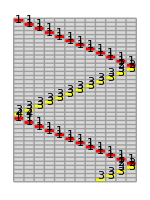
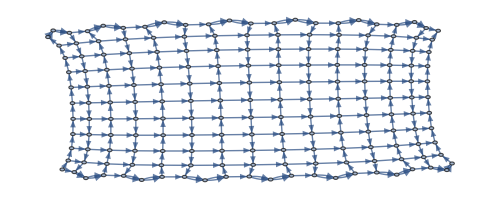
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","AB"->"AC","AC"->"CA","CA"->"BA"},"BAAAAAAAAAAA",200,SSSMax->40,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->179,VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
GuessDimension[%162]
```

Repeating

#### This related ruleset changes width depending on the number of Bs, and edge behavior depending on the number of As, but is still one-dimensional:

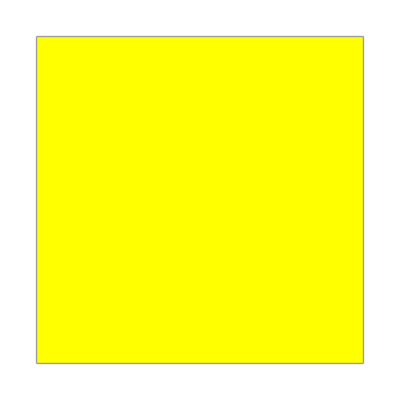

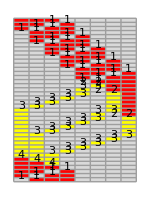
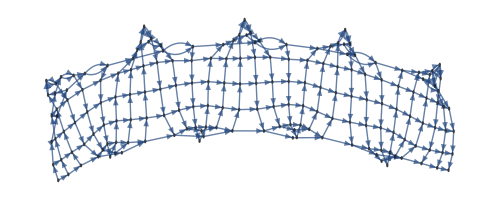
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","AB"->"AC","AC"->"CA","C"->"B"},"BBBAAAAA",200,SSSMax->40,NetMax->177,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->179,VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
SSSDisplay[%31,SSSMax->40,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,NetMax->177,VertexLabels->{x_:>Placed[x,Tooltip],1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}]
```

#### It’s not necessary to do the diagonal retrace to restart, since a new rule can simply restart the next right diagonal.

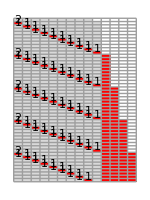
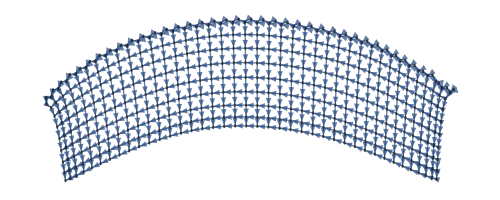
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","A"->"BA"},"AAAAAAAAA",400,SSSMax->50,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
GuessDimension[%189]//Column
```

Set::write: Tag Out in %189 is Protected.

1D

{1D,{1,0,38,10},2
10,2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92 | 102 | 112 | 122 | 132 | 142 | 152 | 162 | 172 | 182 | 192 | 202 | 212 | 222 | 232 | 242 | 252 | 262 | 272 | 282 | 292 | 302 | 312 | 322 | 332 | 342 | 352 | 362 | 372 | 382
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | }
{1D,{1,0,39,10},1
10,1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91 | 101 | 111 | 121 | 131 | 141 | 151 | 161 | 171 | 181 | 191 | 201 | 211 | 221 | 231 | 241 | 251 | 261 | 271 | 281 | 291 | 301 | 311 | 321 | 331 | 341 | 351 | 361 | 371 | 381 | 391
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | }
{1D,{1,1,38,10},13
10,11 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93 | 103 | 113 | 123 | 133 | 143 | 153 | 163 | 173 | 183 | 193 | 203 | 213 | 223 | 233 | 243 | 253 | 263 | 273 | 283 | 293 | 303 | 313 | 323 | 333 | 343 | 353 | 363 | 373 | 383 | 393
2 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | }

```mathematica
MaxStateLengthPositions[%179]
```

{2,12,22,32,42,52,62,72,82,92,102,112,122,132,142,152,162,172,182,192,202,212,222,232}

```mathematica
LeastUsedRulePositions[%179]
```

{1,11,21,31,41,51,61,71,81,91,101,111,121,131,141,151,161,171,181,191,201,211,221,231,241}

```mathematica
DistanceLastPositions[%179]
```

{11,13,23,33,43,53,63,73,83,93,103,113,123,133,143,153,163,173,183,193,203,213,223,233,243}

```mathematica
CheckDimension@DistanceTally[%179]
```

{failed,1 | 2 | 4 | 7 | 11 | 16 | 23 | 31 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120 | 130 | 140 | 150 | 160 | 170 | 180 | 190 | 200 | 210 | 220
1 | 2 | 3 | 4 | 5 | 7 | 8 | 9 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 
1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 1 | -2 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 1 | -3 | 3 | -1 | -1 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  | 
1 | -4 | 6 | -4 | 0 | 3 | -3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  | 
-5 | 10 | -10 | 4 | 3 | -6 | 4 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  | 
15 | -20 | 14 | -1 | -9 | 10 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  | 
-35 | 34 | -15 | -8 | 19 | -15 | 6 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 
69 | -49 | 7 | 27 | -34 | 21 | -7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  | 
-118 | 56 | 20 | -61 | 55 | -28 | 8 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  | 
174 | -36 | -81 | 116 | -83 | 36 | -9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  | 
-210 | -45 | 197 | -199 | 119 | -45 | 10 | -1 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
165 | 242 | -396 | 318 | -164 | 55 | -11 | 1 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
77 | -638 | 714 | -482 | 219 | -66 | 12 | -1 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-715 | 1352 | -1196 | 701 | -285 | 78 | -13 | 1 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2067 | -2548 | 1897 | -986 | 363 | -91 | 14 | -1 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-4615 | 4445 | -2883 | 1349 | -454 | 105 | -15 | 1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9060 | -7328 | 4232 | -1803 | 559 | -120 | 16 | -1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-16388 | 11560 | -6035 | 2362 | -679 | 136 | -17 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
27948 | -17595 | 8397 | -3041 | 815 | -153 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-45543 | 25992 | -11438 | 3856 | -968 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
71535 | -37430 | 15294 | -4824 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[%179[["Net"]]]
```

{1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},1·{{1,9}},7·{{1,10}},1·{{10}},1·{{1,1}},8·{{1}}}

#### 2-d: Incrementing the number of As at the beginning of each diagonal stroke turns the constant width band into a 2-d case.

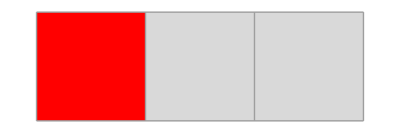
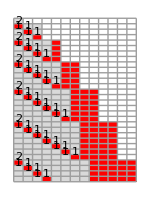
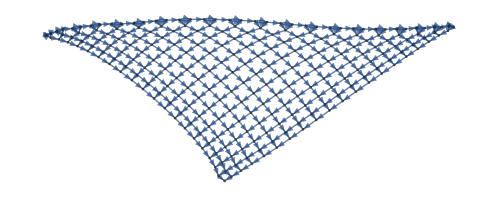
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","A"->"BAA"},"A",250,SSSMax->30,SSSSize->{150,200},NetSize->{500,200},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

```mathematica
GuessDimension[%165]
```

2D

```mathematica
{{"2D",{1,0,17,1},{{2}, {3}, {1}},{{2, 5, 9, 14, 20, 27, 35, 44, 54, 65, 77, 90, 104, 119, 135, 152, 170, 189, 209}, {3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, }, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, , }}},{"2D",{1,0,18,1},{{1}, {3}, {1}},{{1, 4, 8, 13, 19, 26, 34, 43, 53, 64, 76, 89, 103, 118, 134, 151, 169, 188, 208, 229}, {3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, }, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, , }}},{"2D",{1,0,17,1},{{3}, {4}, {1}},{{3, 7, 12, 18, 25, 33, 42, 52, 63, 75, 88, 102, 117, 133, 150, 168, 187, 207, 228}, {4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, }, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, , }}},{"2D",{2,0,17,},{{1, 3}, {2, 2}, {0, 1}},{{1, 3, 5, 8, 11, 15, 19, 24, 29, 35, 41, 48, 55, 63, 71, 80, 89, 99, 109, 120}, {2, 2, 3, 3, 4, 4, 5, 5, 6, 6, 7, 7, 8, 8, 9, 9, 10, 10, 11, }, {0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, , }}}}
```

```mathematica
ToNetDifferenceSets[%165[["Net"]]]
```

{{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5},{5},{1,1,2},{1,4},{1,6},{1,6},{6},{1,1,2},{1,5},{1,7},{1,7},{1,7},{7},{1,1,2},{1,6},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{1,7},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{1,8},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{1,9},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{1,10},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{1,11},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,1,2},{1,12},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14},{1,1,2},{1,13},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15},{1,1,2},{1,14},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16},{1,1,2},{1,15},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17},{1,1,2},{1,16},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18},{1,1,2},{1,17},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19},{1,1,2},{1,18},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20},{1,1,2},{1,19},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21},{1,1,2},{1,20},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22},{1,1,2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
ToReducedNetDifferenceSets[%]
```

```mathematica
{1·{{1,1,2}},1·{{1,2}},1·{{4}},1·{{1,1,2}},1·{{1,3}},1·{{1,5}},1·{{5}},1·{{1,1,2}},1·{{1,4}},2·{{1,6}},1·{{6}},1·{{1,1,2}},1·{{1,5}},3·{{1,7}},1·{{7}},1·{{1,1,2}},1·{{1,6}},4·{{1,8}},1·{{8}},1·{{1,1,2}},1·{{1,7}},5·{{1,9}},1·{{9}},1·{{1,1,2}},1·{{1,8}},6·{{1,10}},1·{{10}},1·{{1,1,2}},1·{{1,9}},7·{{1,11}},1·{{11}},1·{{1,1,2}},1·{{1,10}},8·{{1,12}},1·{{12}},1·{{1,1,2}},1·{{1,11}},9·{{1,13}},1·{{13}},1·{{1,1,2}},1·{{1,12}},10·{{1,14}},1·{{14}},1·{{1,1,2}},1·{{1,13}},11·{{1,15}},1·{{15}},1·{{1,1,2}},1·{{1,14}},12·{{1,16}},1·{{16}},1·{{1,1,2}},1·{{1,15}},13·{{1,17}},1·{{17}},1·{{1,1,2}},1·{{1,16}},14·{{1,18}},1·{{18}},1·{{1,1,2}},1·{{1,17}},15·{{1,19}},1·{{19}},1·{{1,1,2}},1·{{1,18}},16·{{1,20}},1·{{20}},1·{{1,1,2}},1·{{1,19}},17·{{1,21}},1·{{21}},1·{{1,1,2}},1·{{1,20}},18·{{1,22}},1·{{22}},1·{{1,1,2}},...}
```

#### Exponential: Adding an extra A at the beginning of each diagonal stroke makes each pass one step longer, and turns the network into an exponential case.


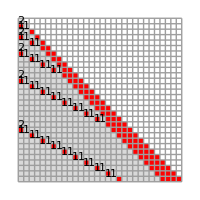
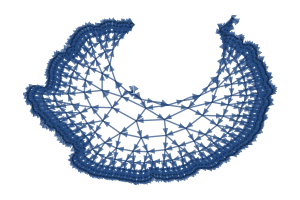
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AAB","A"->"BA"},"A",850,SSSMax->30,SSSSize->{200,200},NetSize->{300,200},RulePlacement->Left,
VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[%171]
```

Set::write: Tag Out in %171 is Protected.

exp

{{exp,{1,0,6,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{1,0,7,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{1,0,6,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134 | 263 | 520
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{2,0,6,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89 | 175 | 346
1 | 2 | 3 | 6 | 11 | 22 | 43 | 86 | 171 | 
1 | 1 | 3 | 5 | 11 | 21 | 43 | 85 |  | }}

```mathematica
NestList[Differences,{1,2,4,7,13,24,46,89,175,346},9]//Column
```

{1,2,4,7,13,24,46,89,175,346}
{1,2,3,6,11,22,43,86,171}
{1,1,3,5,11,21,43,85}
{0,2,2,6,10,22,42}
{2,0,4,4,12,20}
{-2,4,0,8,8}
{6,-4,8,0}
{-10,12,-8}
{22,-20}
{-42}

```mathematica
ToNetDifferenceSets[%171[["Net"]]]
```

{{1,1},{1,3},{1,1},{1,2,4},{4,5},{1,1},{1,4,6},{1,6,7},{1,7,8},{8,9},{1,1},{1,8,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17},{1,1},{1,16,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{32,33},{1,1},{1,32,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{64,65},{1,1},{1,64,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{1,127,128},{128,129},{1,1},{1,128,130},{1,130,131},{1,131,132},{1,132,133},{1,133,134},{1,134,135},{1,135,136},{1,136,137},{1,137,138},{1,138,139},{1,139,140},{1,140,141},{1,141,142},{1,142,143},{1,143,144},{1,144,145},{1,145,146},{1,146,147},{1,147,148},{1,148,149},{1,149,150},{1,150,151},{1,151,152},{1,152,153},{1,153,154},{1,154,155},{1,155,156},{1,156,157},{1,157,158},{1,158,159},{1,159,160},{1,160,161},{1,161,162},{1,162,163},{1,163,164},{1,164,165},{1,165,166},{1,166,167},{1,167,168},{1,168,169},{1,169,170},{1,170,171},{1,171,172},{1,172,173},{1,173,174},{1,174,175},{1,175,176},{1,176,177},{1,177,178},{1,178,179},{1,179,180},{1,180,181},{1,181,182},{1,182,183},{1,183,184},{1,184,185},{1,185,186},{1,186,187},{1,187,188},{1,188,189},{1,189,190},{1,190,191},{1,191,192},{1,192,193},{1,193,194},{1,194,195},{1,195,196},{1,196,197},{1,197,198},{1,198,199},{1,199,200},{1,200,201},{1,201,202},{1,202,203},{1,203,204},{1,204,205},{1,205,206},{1,206,207},{1,207,208},{1,208,209},{1,209,210},{1,210,211},{1,211,212},{1,212,213},{1,213,214},{1,214,215},{1,215,216},{1,216,217},{1,217,218},{1,218,219},{1,219,220},{1,220,221},{1,221,222},{1,222,223},{1,223,224},{1,224,225},{1,225,226},{1,226,227},{1,227,228},{1,228,229},{1,229,230},{1,230,231},{1,231,232},{1,232,233},{1,233,234},{1,234,235},{1,235,236},{1,236,237},{1,237,238},{1,238,239},{1,239,240},{1,240,241},{1,241,242},{1,242,243},{1,243,244},{1,244,245},{1,245,246},{1,246,247},{1,247,248},{1,248,249},{1,249,250},{1,250,251},{1,251,252},{1,252,253},{1,253,254},{1,254,255},{1,255,256},{256,257},{1,1},{1,256,258},{1,258,259},{1,259,260},{1,260,261},{1,261,262},{1,262,263},{1,263,264},{1,264,265},{1,265,266},{1,266,267},{1,267,268},{1,268,269},{1,269,270},{1,270,271},{1,271,272},{1,272,273},{1,273,274},{1,274,275},{1,275,276},{1,276,277},{1,277,278},{1,278,279},{1,279,280},{1,280,281},{1,281,282},{1,282,283},{1,283,284},{1,284,285},{1,285,286},{1,286,287},{1,287,288},{1,288,289},{1,289,290},{1,290,291},{1,291,292},{1,292,293},{1,293,294},{1,294,295},{1,295,296},{1,296,297},{1,297,298},{1,298,299},{1,299,300},{1,300,301},{1,301,302},{1,302,303},{1,303,304},{1,304,305},{1,305,306},{1,306,307},{1,307,308},{1,308,309},{1,309,310},{1,310,311},{1,311,312},{1,312,313},{1,313,314},{1,314,315},{1,315,316},{1,316,317},{1,317,318},{1,318,319},{1,319,320},{1,320,321},{1,321,322},{1,322,323},{1,323,324},{1,324,325},{1,325,326},{1,326,327},{1,327,328},{1,328,329},{1,329,330},{1,330,331},{1,331,332},{1,332,333},{1,333,334},{1,334,335},{1,335,336},{1,336,337},{1,337,338},{1,338,339},{1,339,340},{1,340,341},{1,341,342},{1,342,343},{1,343,344},{1,344,345},{1,345,346},{1,346,347},{1,347,348},{1,348,349},{1,349,350},{1,350,351},{1,351,352},{1,352,353},{1,353,354},{1,354,355},{1,355,356},{1,356,357},{1,357,358},{1,358,359},{1,359,360},{1,360,361},{1,361,362},{1,362,363},{1,363,364},{1,364,365},{1,365,366},{1,366,367},{1,367,368},{1,368,369},{1,369,370},{1,370,371},{1,371,372},{1,372,373},{1,373,374},{1,374,375},{1,375,376},{1,376,377},{1,377,378},{1,378,379},{1,379,380},{1,380,381},{1,381,382},{1,382,383},{1,383,384},{1,384,385},{1,385,386},{1,386,387},{1,387,388},{1,388,389},{1,389,390},{1,390,391},{1,391,392},{1,392,393},{1,393,394},{1,394,395},{1,395,396},{1,396,397},{1,397,398},{1,398,399},{1,399,400},{1,400,401},{1,401,402},{1,402,403},{1,403,404},{1,404,405},{1,405,406},{1,406,407},{1,407,408},{1,408,409},{1,409,410},{1,410,411},{1,411,412},{1,412,413},{1,413,414},{1,414,415},{1,415,416},{1,416,417},{1,417,418},{1,418,419},{1,419,420},{1,420,421},{1,421},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1,1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
|
```

#### 3-d: The constant increase can be changed to a linearly increasing effect by incrementing the number of As whenever the diagonal stroke passes a vertical bar (C), and adding in a new C at the beginning of each diagonal stroke. The entire network is now 3-dimensional.

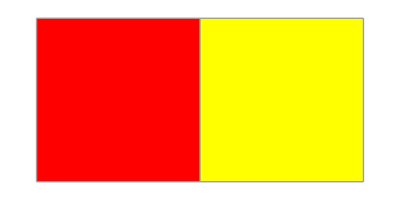
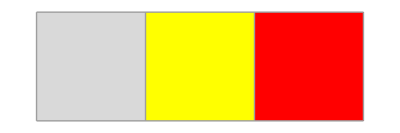
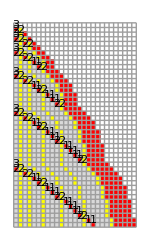
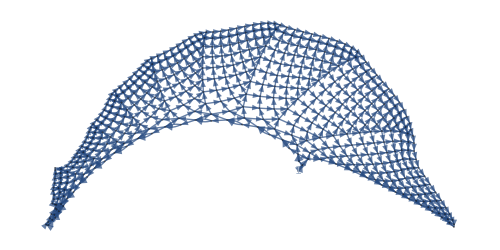
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss3d=SSS[{"BA"->"AB","BC"->"ACB","A"->"BC"},"A",500,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[%177]
```

Set::write: Tag Out in %177 is Protected.

3D

{{3D,{1,0,10,1},6
5
3
1,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391 | 484
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{1,0,10,1},6
5
3
1,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391 | 484
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{1,0,9,1},5
5
3
1,5 | 10 | 18 | 30 | 47 | 70 | 100 | 138 | 185 | 242 | 310 | 390
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{2,0,10,1/2},1 | 2
1 | 2
1 | 1
0 | 1,1 | 2 | 4 | 7 | 12 | 19 | 29 | 42 | 59 | 80 | 106 | 137 | 174 | 217
1 | 2 | 3 | 5 | 7 | 10 | 13 | 17 | 21 | 26 | 31 | 37 | 43 | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 |  | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 |  |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[%177[["Net"]]]
```

{1·{{1,1}},1·{{1,3}},1·{{1,1}},1·{{1,2,4}},1·{{4,5}},1·{{1,1}},1·{{1,4,6}},1·{{1,6,7}},1·{{1,7}},1·{{7,8}},1·{{1,1}},1·{{1,7,9}},1·{{1,9,10}},1·{{1,10}},1·{{1,10,11}},2·{{1,11}},1·{{11,12}},1·{{1,1}},1·{{1,11,13}},1·{{1,13,14}},1·{{1,14}},1·{{1,14,15}},2·{{1,15}},1·{{1,15,16}},3·{{1,16}},1·{{16,17}},1·{{1,1}},1·{{1,16,18}},1·{{1,18,19}},1·{{1,19}},1·{{1,19,20}},2·{{1,20}},1·{{1,20,21}},3·{{1,21}},1·{{1,21,22}},4·{{1,22}},1·{{22,23}},1·{{1,1}},1·{{1,22,24}},1·{{1,24,25}},1·{{1,25}},1·{{1,25,26}},2·{{1,26}},1·{{1,26,27}},3·{{1,27}},1·{{1,27,28}},4·{{1,28}},1·{{1,28,29}},5·{{1,29}},1·{{29,30}},1·{{1,1}},1·{{1,29,31}},1·{{1,31,32}},1·{{1,32}},1·{{1,32,33}},2·{{1,33}},1·{{1,33,34}},3·{{1,34}},1·{{1,34,35}},4·{{1,35}},1·{{1,35,36}},5·{{1,36}},1·{{1,36,37}},6·{{1,37}},1·{{37,38}},1·{{1,1}},1·{{1,37,39}},1·{{1,39,40}},1·{{1,40}},1·{{1,40,41}},2·{{1,41}},1·{{1,41,42}},3·{{1,42}},1·{{1,42,43}},4·{{1,43}},1·{{1,43,44}},5·{{1,44}},1·{{1,44,45}},6·{{1,45}},1·{{1,45,46}},7·{{1,46}},1·{{46,47}},1·{{1,1}},1·{{1,46,48}},1·{{1,48,49}},1·{{1,49}},1·{{1,49,50}},2·{{1,50}},1·{{1,50,51}},3·{{1,51}},1·{{1,51,52}},4·{{1,52}},1·{{1,52,53}},5·{{1,53}},1·{{1,53,54}},6·{{1,54}},1·{{1,54,55}},7·{{1,55}},1·{{1,55,56}},8·{{1,56}},1·{{56,57}},1·{{1,1}},1·{{1,56,58}},1·{{1,58,59}},1·{{1,59}},1·{{1,59,60}},2·{{1,60}},1·{{1,60,61}},3·{{1,61}},1·{{1,61,62}},4·{{1,62}},1·{{1,62,63}},5·{{1,63}},1·{{1,63,64}},6·{{1,64}},1·{{1,64,65}},7·{{1,65}},1·{{1,65,66}},8·{{1,66}},1·{{1,66,67}},9·{{1,67}},1·{{67,68}},1·{{1,1}},1·{{1,67,69}},1·{{1,69,70}},1·{{1,70}},1·{{1,70,71}},2·{{1,71}},1·{{1,71,72}},3·{{1,72}},1·{{1,72,73}},4·{{1,73}},1·{{1,73,74}},5·{{1,74}},1·{{1,74,75}},6·{{1,75}},1·{{1,75,76}},7·{{1,76}},1·{{1,76,77}},8·{{1,77}},1·{{1,77,78}},9·{{1,78}},1·{{1,78,79}},10·{{1,79}},1·{{79,80}},1·{{1,1}},1·{{1,79,81}},1·{{1,81,82}},1·{{1,82}},1·{{1,82,83}},2·{{1,83}},1·{{1,83,84}},3·{{1,84}},1·{{1,84,85}},4·{{1,85}},1·{{1,85,86}},5·{{1,86}},1·{{1,86,87}},6·{{1,87}},1·{{1,87,88}},7·{{1,88}},1·{{1,88,89}},8·{{1,89}},1·{{1,89,90}},9·{{1,90}},1·{{1,90,91}},10·{{1,91}},1·{{1,91,92}},11·{{1,92}},1·{{92,93}},1·{{1,1}},1·{{1,92,94}},1·{{1,94,95}},1·{{1,95}},1·{{1,95,96}},2·{{1,96}},1·{{1,96,97}},3·{{1,97}},1·{{1,97,98}},80·{{1}},1·{{}},1·{{1,1}},15·{{1}}}

```mathematica
SSSAnimate[sss3d]
```

#### 4-d: A quadratic increase is achieved by creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, and an A whenever it passes a D. The entire network is now 4-dimensional.

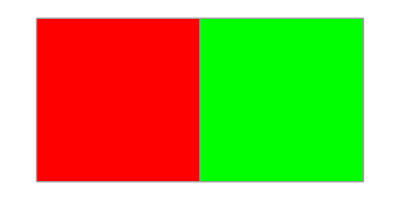
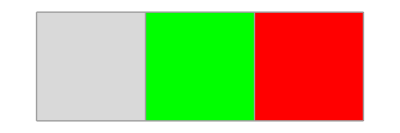
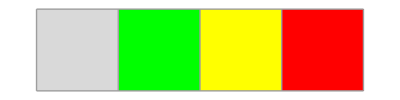
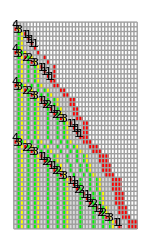
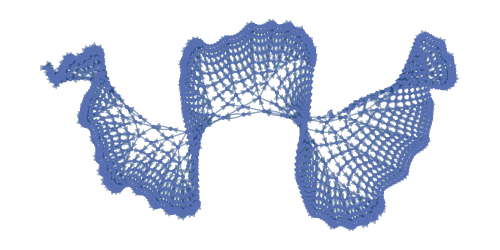
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss4d=SSS[{"BA"->"AB","BD"->"ADB","BC"->"ADCB","A"->"BC"},"AAAA",1500,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sss4d]
```

{{4D,{1,0,8,1},3
7
5
4
1,3 | 10 | 22 | 43 | 78 | 133 | 215 | 332 | 493 | 708 | 988 | 1345
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 215 | 280 | 357 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 |  | 
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{1,0,8,1},6
7
5
4
1,6 | 13 | 25 | 46 | 81 | 136 | 218 | 335 | 496 | 711 | 991 | 1348
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 215 | 280 | 357 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 |  | 
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{1,0,8,1},2
7
5
4
1,2 | 9 | 21 | 42 | 77 | 132 | 214 | 331 | 492 | 707 | 987 | 1344
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 215 | 280 | 357 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 |  | 
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{2,3,5,1/2},14 | 29
15 | 23
8 | 12
4 | 3
-1 | 2,1 | 2 | 6 | 14 | 29 | 52 | 87 | 137 | 207 | 301 | 425 | 584 | 785
1 | 4 | 8 | 15 | 23 | 35 | 50 | 70 | 94 | 124 | 159 | 201 | 
3 | 4 | 7 | 8 | 12 | 15 | 20 | 24 | 30 | 35 | 42 |  | 
1 | 3 | 1 | 4 | 3 | 5 | 4 | 6 | 5 | 7 |  |  | 
2 | -2 | 3 | -1 | 2 | -1 | 2 | -1 | 2 |  |  |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss4d[["Net"]]]
```

{{1,1},{1,4,6,7},2·{{1,7}},{7},{1,1},{1,6,8,9},{1,9,10},{1,10,11,12},2·{{1,12}},{12},{1,1},{1,11,13,14},{1,14,15},{1,15,16,17},{1,17},{1,17,18},{1,18},{1,18,19},{1,19,20,21},2·{{1,21}},{21},{1,1},{1,20,22,23},{1,23,24},{1,24,25,26},{1,26},{1,26,27},{1,27},{1,27,28},{1,28,29,30},2·{{1,30}},{1,30,31},2·{{1,31}},{1,31,32},{1,32},{1,32,33},{1,33,34,35},2·{{1,35}},{35},{1,1},{1,34,36,37},{1,37,38},{1,38,39,40},{1,40},{1,40,41},{1,41},{1,41,42},{1,42,43,44},2·{{1,44}},{1,44,45},2·{{1,45}},{1,45,46},{1,46},{1,46,47},{1,47,48,49},3·{{1,49}},{1,49,50},3·{{1,50}},{1,50,51},2·{{1,51}},{1,51,52},{1,52},{1,52,53},{1,53,54,55},2·{{1,55}},{55},{1,1},{1,54,56,57},{1,57,58},{1,58,59,60},{1,60},{1,60,61},{1,61},{1,61,62},{1,62,63,64},2·{{1,64}},{1,64,65},2·{{1,65}},{1,65,66},{1,66},{1,66,67},{1,67,68,69},3·{{1,69}},{1,69,70},3·{{1,70}},{1,70,71},2·{{1,71}},{1,71,72},{1,72},{1,72,73},{1,73,74,75},4·{{1,75}},{1,75,76},4·{{1,76}},{1,76,77},3·{{1,77}},{1,77,78},2·{{1,78}},{1,78,79},{1,79},{1,79,80},{1,80,81,82},2·{{1,82}},{82},{1,1},{1,81,83,84},{1,84,85},{1,85,86,87},{1,87},{1,87,88},{1,88},{1,88,89},{1,89,90,91},2·{{1,91}},{1,91,92},2·{{1,92}},{1,92,93},{1,93},{1,93,94},{1,94,95,96},3·{{1,96}},{1,96,97},3·{{1,97}},{1,97,98},2·{{1,98}},{1,98,99},{1,99},{1,99,100},{1,100,101,102},4·{{1,102}},{1,102,103},4·{{1,103}},{1,103,104},3·{{1,104}},{1,104,105},2·{{1,105}},{1,105,106},{1,106},{1,106,107},{1,107,108,109},5·{{1,109}},{1,109,110},5·{{1,110}},{1,110,111},4·{{1,111}},{1,111,112},3·{{1,112}},{1,112,113},2·{{1,113}},{1,113,114},{1,114},{1,114,115},{1,115,116,117},2·{{1,117}},{117},{1,1},{1,116,118,119},{1,119,120},{1,120,121,122},{1,122},{1,122,123},{1,123},{1,123,124},{1,124,125,126},2·{{1,126}},{1,126,127},2·{{1,127}},{1,127,128},{1,128},{1,128,129},{1,129,130,131},3·{{1,131}},{1,131,132},3·{{1,132}},{1,132,133},2·{{1,133}},{1,133,134},{1,134},{1,134,135},{1,135,136,137},4·{{1,137}},{1,137,138},4·{{1,138}},{1,138,139},3·{{1,139}},{1,139,140},2·{{1,140}},{1,140,141},{1,141},{1,141,142},{1,142,143,144},5·{{1,144}},{1,144,145},5·{{1,145}},{1,145,146},4·{{1,146}},{1,146,147},3·{{1,147}},{1,147,148},2·{{1,148}},{1,148,149},{1,149},{1,149,150},{1,150,151,152},6·{{1,152}},{1,152,153},6·{{1,153}},{1,153,154},5·{{1,154}},{1,154,155},4·{{1,155}},{1,155,156},3·{{1,156}},{1,156,157},2·{{1,157}},{1,157,158},{1,158},{1,158,159},{1,159,160,161},2·{{1,161}},{161},{1,1},{1,160,162,163},{1,163,164},{1,164,165,166},{1,166},{1,166,167},{1,167},{1,167,168},{1,168,169,170},2·{{1,170}},{1,170,171},2·{{1,171}},{1,171,172},{1,172},{1,172,173},{1,173,174,175},3·{{1,175}},{1,175,176},3·{{1,176}},{1,176,177},2·{{1,177}},{1,177,178},{1,178},{1,178,179},{1,179,180,181},4·{{1,181}},{1,181,182},4·{{1,182}},{1,182,183},3·{{1,183}},{1,183,184},2·{{1,184}},{1,184,185},{1,185},{1,185,186},{1,186,187,188},5·{{1,188}},{1,188,189},5·{{1,189}},{1,189,190},4·{{1,190}},{1,190,191},3·{{1,191}},{1,191,192},2·{{1,192}},{1,192,193},{1,193},{1,193,194},{1,194,195,196},6·{{1,196}},{1,196,197},6·{{1,197}},{1,197,198},5·{{1,198}},{1,198,199},4·{{1,199}},{1,199,200},3·{{1,200}},{1,200,201},2·{{1,201}},{1,201,202},{1,202},{1,202,203},{1,203,204,205},7·{{1,205}},{1,205,206},7·{{1,206}},{1,206,207},6·{{1,207}},{1,207,208},5·{{1,208}},{1,208,209},4·{{1,209}},{1,209,210},3·{{1,210}},{1,210,211},2·{{1,211}},{1,211,212},{1,212},{1,212,213},{1,213,214,215},2·{{1,215}},{215},{1,1},{1,214,216,217},{1,217,218},{1,218,219,220},{1,220},{1,220,221},{1,221},{1,221,222},{1,222,223,224},2·{{1,224}},{1,224,225},2·{{1,225}},{1,225,226},{1,226},{1,226,227},{1,227,228,229},3·{{1,229}},{1,229,230},3·{{1,230}},{1,230,231},2·{{1,231}},{1,231,232},{1,232},{1,232,233},{1,233,234,235},4·{{1,235}},{1,235,236},4·{{1,236}},{1,236,237},3·{{1,237}},{1,237,238},2·{{1,238}},{1,238,239},{1,239},{1,239,240},{1,240,241,242},5·{{1,242}},{1,242,243},5·{{1,243}},{1,243,244},4·{{1,244}},{1,244,245},3·{{1,245}},{1,245,246},2·{{1,246}},{1,246,247},{1,247},{1,247,248},{1,248,249,250},6·{{1,250}},{1,250,251},6·{{1,251}},{1,251,252},5·{{1,252}},{1,252,253},4·{{1,253}},{1,253,254},3·{{1,254}},{1,254,255},2·{{1,255}},{1,255,256},{1,256},{1,256,257},{1,257,258,259},7·{{1,259}},{1,259,260},7·{{1,260}},{1,260,261},6·{{1,261}},{1,261,262},5·{{1,262}},{1,262,263},4·{{1,263}},{1,263,264},3·{{1,264}},{1,264,265},2·{{1,265}},{1,265,266},{1,266},{1,266,267},{1,267,268,269},8·{{1,269}},{1,269,270},8·{{1,270}},{1,270,271},7·{{1,271}},{1,271,272},6·{{1,272}},{1,272,273},5·{{1,273}},{1,273,274},4·{{1,274}},{1,274,275},3·{{1,275}},{1,275,276},2·{{1,276}},{1,276,277},{1,277},{1,277,278},{1,278,279,280},2·{{1,280}},{280},{1,1},{1,279,281,282},{1,282,283},{1,283,284,285},{1,285},{1,285,286},{1,286},{1,286,287},{1,287,288,289},2·{{1,289}},{1,289,290},2·{{1,290}},{1,290,291},{1,291},{1,291,292},{1,292,293,294},3·{{1,294}},{1,294,295},3·{{1,295}},{1,295,296},2·{{1,296}},{1,296,297},{1,297},{1,297,298},{1,298,299,300},4·{{1,300}},{1,300,301},4·{{1,301}},{1,301,302},3·{{1,302}},{1,302,303},2·{{1,303}},{1,303,304},{1,304},{1,304,305},{1,305,306,307},5·{{1,307}},{1,307,308},5·{{1,308}},{1,308,309},4·{{1,309}},{1,309,310},3·{{1,310}},{1,310,311},2·{{1,311}},{1,311,312},{1,312},{1,312,313},{1,313,314,315},6·{{1,315}},{1,315,316},6·{{1,316}},{1,316,317},5·{{1,317}},{1,317,318},4·{{1,318}},{1,318,319},3·{{1,319}},{1,319,320},2·{{1,320}},{1,320,321},{1,321},{1,321,322},{1,322,323,324},7·{{1,324}},{1,324,325},7·{{1,325}},{1,325,326},6·{{1,326}},{1,326,327},5·{{1,327}},{1,327,328},4·{{1,328}},{1,328,329},3·{{1,329}},{1,329,330},2·{{1,330}},{1,330,331},{1,331},{1,331,332},{1,332,333,334},8·{{1,334}},{1,334,335},8·{{1,335}},{1,335,336},7·{{1,336}},{1,336,337},6·{{1,337}},{1,337,338},5·{{1,338}},{1,338,339},4·{{1,339}},{1,339,340},3·{{1,340}},{1,340,341},2·{{1,341}},{1,341,342},{1,342},{1,342,343},{1,343,344,345},9·{{1,345}},{1,345,346},9·{{1,346}},{1,346,347},8·{{1,347}},{1,347,348},7·{{1,348}},{1,348,349},6·{{1,349}},{1,349,350},5·{{1,350}},{1,350,351},4·{{1,351}},{1,351,352},3·{{1,352}},{1,352,353},2·{{1,353}},{1,353,354},{1,354},{1,354,355},{1,355,356,357},2·{{1,357}},{357},{1,1},{1,356,358,359},{1,359,360},{1,360,361,362},{1,362},{1,362,363},{1,363},{1,363,364},{1,364,365,366},2·{{1,366}},{1,366,367},2·{{1,367}},{1,367,368},{1,368},{1,368,369},{1,369,370,371},3·{{1,371}},{1,371,372},3·{{1,372}},{1,372,373},2·{{1,373}},{1,373,374},{1,374},{1,374,375},{1,375,376,377},4·{{1,377}},{1,377,378},4·{{1,378}},{1,378,379},3·{{1,379}},{1,379,380},2·{{1,380}},{1,380,381},{1,381},{1,381,382},{1,382,383,384},5·{{1,384}},{1,384,385},5·{{1,385}},{1,385,386},4·{{1,386}},{1,386,387},3·{{1,387}},{1,387,388},2·{{1,388}},{1,388,389},{1,389},{1,389,390},{1,390,391,392},6·{{1,392}},{1,392,393},6·{{1,393}},{1,393,394},5·{{1,394}},{1,394,395},4·{{1,395}},{1,395,396},3·{{1,396}},{1,396,397},2·{{1,397}},{1,397,398},{1,398},244·{{1}},{},{1,1},151·{{1}}}

#### 5-d: Creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, an E whenever the diagonal stroke passes a D, and an A whenever it passes an E. The entire network is now 5-dimensional.

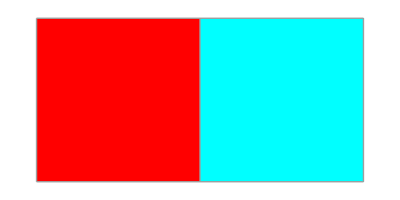
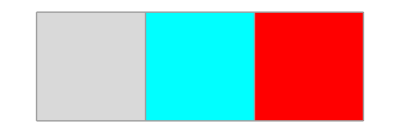
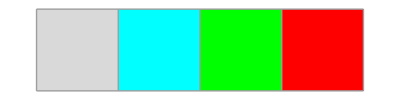
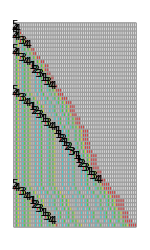
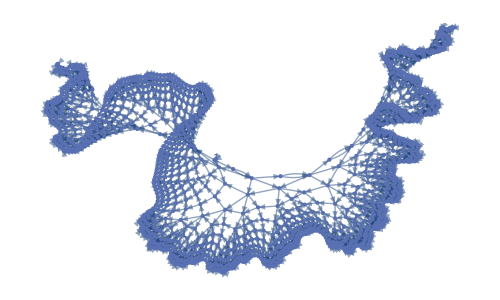
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss5d=SSS[{"BA"->"AB","BE"->"AEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",1500,SSSMax->50,SSSSize->{150,250},NetSize->{500,300},RulePlacement->Left,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sss5d]
```

Part::partw: Part 1 of {} does not exist.

{}

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss5d[["Net"]]]
```

{{1,1},{1,3,4},{1,1},{1,3,5,6},{1,6,7,8},{8,9,10},{1,1},{1,9,11,12},{1,12,13,14},{1,14,15,16},{1,16},{1,16,17},{1,17,18,19},{1,19},{1,19,20,21},{21,22,23},{1,1},{1,22,24,25},{1,25,26,27},{1,27,28,29},{1,29},{1,29,30},{1,30,31,32},{1,32},{1,32,33,34},{1,34,35,36},2·{{1,36}},{1,36,37},{1,37},{1,37,38},{1,38,39,40},2·{{1,40}},{1,40,41},{1,41,42,43},{1,43},{1,43,44,45},{45,46,47},{1,1},{1,46,48,49},{1,49,50,51},{1,51,52,53},{1,53},{1,53,54},{1,54,55,56},{1,56},{1,56,57,58},{1,58,59,60},2·{{1,60}},{1,60,61},{1,61},{1,61,62},{1,62,63,64},2·{{1,64}},{1,64,65},{1,65,66,67},{1,67},{1,67,68,69},{1,69,70,71},3·{{1,71}},{1,71,72},2·{{1,72}},{1,72,73},{1,73},{1,73,74},{1,74,75,76},3·{{1,76}},{1,76,77},{1,77},{1,77,78},{1,78,79,80},2·{{1,80}},{1,80,81},{1,81,82,83},{1,83},{1,83,84,85},{85,86,87},{1,1},{1,86,88,89},{1,89,90,91},{1,91,92,93},{1,93},{1,93,94},{1,94,95,96},{1,96},{1,96,97,98},{1,98,99,100},2·{{1,100}},{1,100,101},{1,101},{1,101,102},{1,102,103,104},2·{{1,104}},{1,104,105},{1,105,106,107},{1,107},{1,107,108,109},{1,109,110,111},3·{{1,111}},{1,111,112},2·{{1,112}},{1,112,113},{1,113},{1,113,114},{1,114,115,116},3·{{1,116}},{1,116,117},{1,117},{1,117,118},{1,118,119,120},2·{{1,120}},{1,120,121},{1,121,122,123},{1,123},{1,123,124,125},{1,125,126,127},4·{{1,127}},{1,127,128},3·{{1,128}},{1,128,129},2·{{1,129}},{1,129,130},{1,130},{1,130,131},{1,131,132,133},4·{{1,133}},{1,133,134},2·{{1,134}},{1,134,135},{1,135},{1,135,136},{1,136,137,138},3·{{1,138}},{1,138,139},{1,139},{1,139,140},{1,140,141,142},2·{{1,142}},{1,142,143},{1,143,144,145},{1,145},{1,145,146,147},{147,148,149},{1,1},{1,148,150,151},{1,151,152,153},{1,153,154,155},{1,155},{1,155,156},{1,156,157,158},{1,158},{1,158,159,160},{1,160,161,162},2·{{1,162}},{1,162,163},{1,163},{1,163,164},{1,164,165,166},2·{{1,166}},{1,166,167},{1,167,168,169},{1,169},{1,169,170,171},{1,171,172,173},3·{{1,173}},{1,173,174},2·{{1,174}},{1,174,175},{1,175},{1,175,176},{1,176,177,178},3·{{1,178}},{1,178,179},{1,179},{1,179,180},{1,180,181,182},2·{{1,182}},{1,182,183},{1,183,184,185},{1,185},{1,185,186,187},{1,187,188,189},4·{{1,189}},{1,189,190},3·{{1,190}},{1,190,191},2·{{1,191}},{1,191,192},{1,192},{1,192,193},{1,193,194,195},4·{{1,195}},{1,195,196},2·{{1,196}},{1,196,197},{1,197},{1,197,198},{1,198,199,200},3·{{1,200}},{1,200,201},{1,201},{1,201,202},{1,202,203,204},2·{{1,204}},{1,204,205},{1,205,206,207},{1,207},{1,207,208,209},{1,209,210,211},5·{{1,211}},{1,211,212},4·{{1,212}},{1,212,213},3·{{1,213}},{1,213,214},2·{{1,214}},{1,214,215},{1,215},{1,215,216},{1,216,217,218},5·{{1,218}},{1,218,219},3·{{1,219}},{1,219,220},2·{{1,220}},{1,220,221},{1,221},{1,221,222},{1,222,223,224},4·{{1,224}},{1,224,225},2·{{1,225}},{1,225,226},{1,226},{1,226,227},{1,227,228,229},3·{{1,229}},{1,229,230},{1,230},{1,230,231},{1,231,232,233},2·{{1,233}},{1,233,234},{1,234,235,236},{1,236},{1,236,237,238},{238,239,240},{1,1},{1,239,241,242},{1,242,243,244},{1,244,245,246},{1,246},{1,246,247},{1,247,248,249},{1,249},{1,249,250,251},{1,251,252,253},2·{{1,253}},{1,253,254},{1,254},{1,254,255},{1,255,256,257},2·{{1,257}},{1,257,258},{1,258,259,260},{1,260},{1,260,261,262},{1,262,263,264},3·{{1,264}},{1,264,265},2·{{1,265}},{1,265,266},{1,266},{1,266,267},{1,267,268,269},3·{{1,269}},{1,269,270},{1,270},{1,270,271},{1,271,272,273},2·{{1,273}},{1,273,274},{1,274,275,276},{1,276},{1,276,277,278},{1,278,279,280},4·{{1,280}},{1,280,281},3·{{1,281}},{1,281,282},2·{{1,282}},{1,282,283},{1,283},{1,283,284},{1,284,285,286},4·{{1,286}},{1,286,287},2·{{1,287}},{1,287,288},{1,288},{1,288,289},{1,289,290,291},3·{{1,291}},{1,291,292},{1,292},{1,292,293},{1,293,294,295},2·{{1,295}},{1,295,296},{1,296,297,298},{1,298},{1,298,299,300},{1,300,301,302},5·{{1,302}},{1,302,303},4·{{1,303}},{1,303,304},3·{{1,304}},{1,304,305},2·{{1,305}},{1,305,306},{1,306},{1,306,307},{1,307,308,309},5·{{1,309}},{1,309,310},3·{{1,310}},{1,310,311},2·{{1,311}},{1,311,312},{1,312},{1,312,313},{1,313,314,315},4·{{1,315}},{1,315,316},2·{{1,316}},{1,316,317},{1,317},{1,317,318},{1,318,319,320},3·{{1,320}},{1,320,321},{1,321},{1,321,322},{1,322,323,324},2·{{1,324}},{1,324,325},{1,325,326,327},{1,327},{1,327,328,329},{1,329,330,331},6·{{1,331}},{1,331,332},5·{{1,332}},{1,332,333},4·{{1,333}},{1,333,334},3·{{1,334}},{1,334,335},2·{{1,335}},{1,335,336},{1,336},{1,336,337},{1,337,338,339},6·{{1,339}},{1,339,340},4·{{1,340}},{1,340,341},3·{{1,341}},{1,341,342},2·{{1,342}},{1,342,343},{1,343},{1,343,344},{1,344,345,346},5·{{1,346}},{1,346,347},3·{{1,347}},{1,347,348},2·{{1,348}},{1,348,349},{1,349},{1,349,350},{1,350,351,352},4·{{1,352}},{1,352,353},2·{{1,353}},{1,353,354},{1,354},{1,354,355},{1,355,356,357},3·{{1,357}},{1,357,358},{1,358},{1,358,359},{1,359,360,361},2·{{1,361}},{1,361,362},{1,362,363,364},{1,364},{1,364,365,366},{366,367,368},{1,1},{1,367,369,370},{1,370,371,372},{1,372,373,374},{1,374},{1,374,375},{1,375,376,377},{1,377},{1,377,378,379},{1,379,380,381},2·{{1,381}},{1,381,382},{1,382},{1,382,383},{1,383,384,385},2·{{1,385}},{1,385,386},{1,386,387,388},{1,388},{1,388,389,390},{1,390,391,392},3·{{1,392}},{1,392,393},2·{{1,393}},{1,393,394},{1,394},{1,394,395},{1,395,396,397},3·{{1,397}},{1,397,398},{1,398},{1,398,399},{1,399,400,401},2·{{1,401}},{1,401,402},{1,402,403,404},{1,404},{1,404,405,406},{1,406,407,408},4·{{1,408}},{1,408,409},3·{{1,409}},{1,409,410},2·{{1,410}},{1,410,411},{1,411},{1,411,412},{1,412,413,414},4·{{1,414}},{1,414,415},2·{{1,415}},{1,415,416},{1,416},{1,416,417},{1,417,418,419},3·{{1,419}},{1,419,420},{1,420},{1,420,421},{1,421,422,423},2·{{1,423}},{1,423,424},{1,424,425,426},{1,426},{1,426,427,428},{1,428,429,430},5·{{1,430}},{1,430,431},4·{{1,431}},{1,431,432},3·{{1,432}},{1,432,433},2·{{1,433}},{1,433,434},{1,434},{1,434,435},{1,435,436,437},5·{{1,437}},{1,437,438},3·{{1,438}},{1,438,439},2·{{1,439}},{1,439,440},{1,440},{1,440,441},{1,441,442,443},4·{{1,443}},{1,443,444},2·{{1,444}},{1,444,445},{1,445},{1,445,446},{1,446,447,448},3·{{1,448}},{1,448,449},{1,449},{1,449,450},{1,450,451,452},2·{{1,452}},{1,452,453},{1,453,454,455},{1,455},{1,455,456,457},{1,457,458,459},6·{{1,459}},{1,459,460},5·{{1,460}},{1,460,461},4·{{1,461}},{1,461,462},3·{{1,462}},{1,462,463},2·{{1,463}},{1,463,464},{1,464},{1,464,465},{1,465,466,467},6·{{1,467}},{1,467,468},4·{{1,468}},{1,468,469},3·{{1,469}},{1,469,470},2·{{1,470}},{1,470,471},{1,471},{1,471,472},{1,472,473,474},5·{{1,474}},{1,474,475},3·{{1,475}},{1,475,476},2·{{1,476}},{1,476,477},{1,477},{1,477,478},{1,478,479,480},4·{{1,480}},{1,480,481},2·{{1,481}},{1,481,482},{1,482},{1,482,483},{1,483,484,485},3·{{1,485}},{1,485,486},{1,486},{1,486,487},{1,487,488,489},2·{{1,489}},{1,489,490},{1,490,491,492},{1,492},{1,492,493,494},{1,494,495,496},7·{{1,496}},{1,496,497},6·{{1,497}},{1,497,498},5·{{1,498}},{1,498,499},4·{{1,499}},{1,499,500},3·{{1,500}},{1,500,501},2·{{1,501}},{1,501,502},{1,502},{1,502,503},{1,503,504,505},7·{{1,505}},{1,505,506},5·{{1,506}},{1,506,507},4·{{1,507}},{1,507,508},3·{{1,508}},{1,508,509},2·{{1,509}},{1,509,510},{1,510},{1,510,511},{1,511,512,513},6·{{1,513}},{1,513,514},4·{{1,514}},{1,514,515},3·{{1,515}},{1,515,516},2·{{1,516}},{1,516,517},{1,517},{1,517,518},{1,518,519,520},5·{{1,520}},{1,520,521},3·{{1,521}},{1,521,522},2·{{1,522}},{1,522,523},{1,523},{1,523,524},{1,524,525,526},4·{{1,526}},{1,526,527},2·{{1,527}},{1,527,528},{1,528},{1,528,529},{1,529,530,531},3·{{1,531}},{1,531,532},{1,532},{1,532,533},{1,533,534,535},2·{{1,535}},{1,535,536},{1,536,537,538},{1,538},{1,538,539,540},{540,541,542},{1,1},{1,541,543,544},{1,544,545,546},{1,546,547,548},{1,548},{1,548,549},{1,549,550,551},{1,551},{1,551,552,553},{1,553,554,555},2·{{1,555}},{1,555,556},{1,556},527·{{1}},{},{1,1},26·{{1}}}

#### 6-d

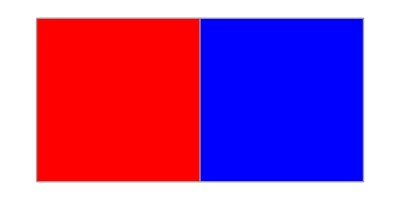
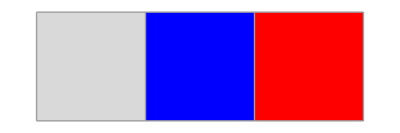
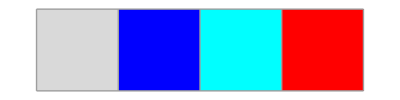
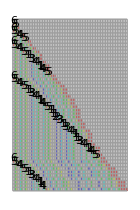
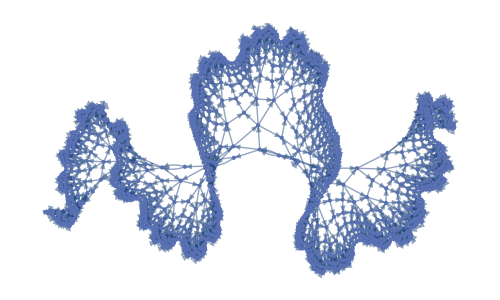
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","BF"->"AFB","BE"->"AFEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",1500,SSSMax->50,SSSSize->{140,210},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

#### Other n-d cases

Try for n-dimensional, without the inert red section at the end:  needs one extra rule:

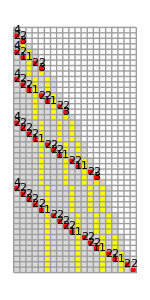
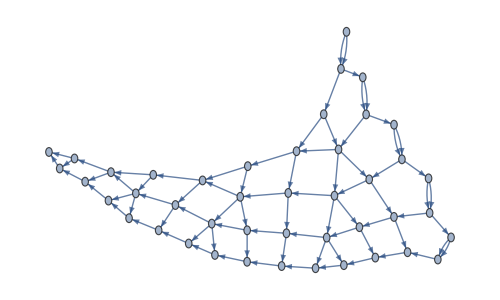
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BC"->"ACB","BA"->"AB","B"->"CA","A"->"BA"},"A",44,SSSSize->{150,300},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

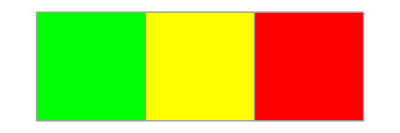
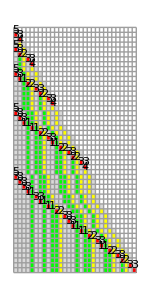
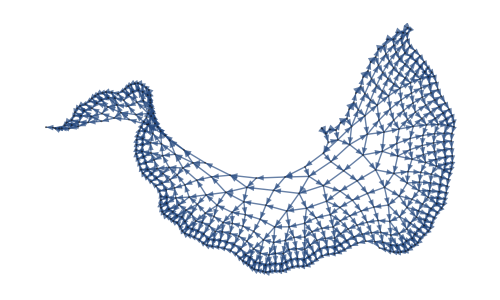
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BD"->"ADB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",500,SSSMax->50,SSSSize->{150,300},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

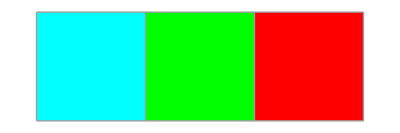
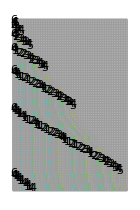
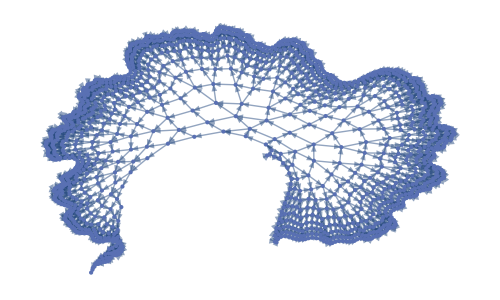
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BE"->"AEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",1500,SSSMax->100,SSSSize->{140,210},NetSize->{500,300},RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```

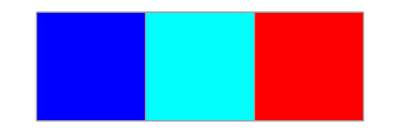
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BF"->"AFB","BE"->"FEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",5100,SSSMax->100,NetMax->700,SSSSize->{140,210},NetSize->{500,300},Mesh->False,RulePlacement->Left,VertexLabels->Placed["Name",Tooltip]];
```